# Visualizing Time-Dependent Scalar and Vector Fields

## Cross Products

Here is the built-in cross product between two vectors

```mathematica
crossab =Cross[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}  ,{Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}]
```

{-a_3 b_2+a_2 b_3,a_3 b_1-a_1 b_3,-a_2 b_1+a_1 b_2}

And, here is the standard visual way to do it by hand with the determinant.

```mathematica
detab =Det[({{i, j, k}, {Subscript[a, 1], Subscript[a, 2], Subscript[a, 3]}, {Subscript[b, 1], Subscript[b, 2], Subscript[b, 3]}})]
```

Pick out each of the compenents to create the vector

```mathematica
testcrossab={Coefficient[detab,i], Coefficient[detab,j],Coefficient[detab,k]}
```

Check for equality between the old-fashioned way and Mathematica's built-in function

```mathematica
testcrossab == crossab
```

testcrossab=={-a_3 b_2+a_2 b_3,a_3 b_1-a_1 b_3,-a_2 b_1+a_1 b_2}

## Visualizing Space Curves as Time-Dependent Vectors

Create a trajectory of a point or a particle

```mathematica
XVector[t_] := {Cos[6 t],Sin[4t ], Sin[t]  + Cos[t]}
```

ParametricPlot3D allows us to visualize the entire trajectory at once.

```mathematica
ParametricPlot3D[XVector[t],{t,0,2 π},PlotStyle-> {Thick, Blue},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

Here is a function to create a graphic with a variable end - point. We will have the function remember when it has already computed a graphic, trading memory for a possible speed-up.

```mathematica
paraplot[time_] :=paraplot[time]= ParametricPlot3D[XVector[t],{t,0,time},PlotStyle-> {Thick, Blue},AxesLabel->{"x","y","z"}]
```

Use manipulate on the graphics function to visualize how the curve develops with its parameter

```mathematica
Manipulate[paraplot[time],{{time,0.05},0.01,2 π}]
```

However, we need to fix the length scale between frames, so we use the last graphic to infer what PlotRange should be.

```mathematica
Manipulate[Show[paraplot[time],PlotRange->{{-1,1},{-1,1},{-1.5,1.5}}],{{time,0.05},0.01,2 π}]
```

Next, we add a graphic element to show the vector, drawn from the origin, for each end-point.

```mathematica
Manipulate[Show[{paraplot[time],Graphics3D[{Cylinder[{{0,0,0},XVector[time]},0.03]}]},PlotRange->{{-1,1},{-1,1},{-1.5,1.5}}],{{time,0.05},0.01,2 π}]
```

## Visualizing Local Tangent Vectors of Space Curves

Compute the local derivative of the vector that we visualized above: v⃗ = (d x⃗)/dt

```mathematica
Simplify[D[XVector[t],t]]
```

{-6 Sin[6 t],4 Cos[4 t],Cos[t]-Sin[t]}

Write out a function for the derivative:

```mathematica
dxdt[s_] :={-6 Sin[6 s],4 Cos[4 s],Cos[s]-Sin[s]}
```

Plot it.... Note that it doesn't "appear" to be periodic, which would be wrong.

```mathematica
dxdtplot[time_] := ParametricPlot3D[dxdt[t],{t,0,time},PlotStyle-> {Thick, Darker[Red]},AxesLabel->{"x","y","z"}]
dxdtplot[2 π]
```

-Graphics3D-

The puzzle can be visualizing the time-development of both curves:

```mathematica
Manipulate[Show[paraplot[time],dxdtplot[time],
Graphics3D[{
{Lighter[Blue],Cylinder[{{0,0,0},XVector[time]},0.1]},
{Lighter[Red],Cylinder[{{0,0,0}, dxdt[time]},0.1]}
}],PlotRange->{{-6,6},{-4,4},{-1.5,1.5}}],{{time,0.05},0.01,2 π}]
```

To visualize the "tangency property,"  we translate the derivative-vector to the end of the space curve

```mathematica
Manipulate[Show[paraplot[time],dxdtplot[time],
Graphics3D[{
{Lighter[Blue],Cylinder[{{0,0,0},XVector[time]},0.1]},
{Lighter[Red],Cylinder[{XVector[time], dxdt[time]},0.1]}
}],PlotRange->{{-6,6},{-6,6},{-4,4}}],{{time,0.05},0.01,2 π}]
```

## The Time-Dependent Solution to the Diffusion Equation in the Plane Rectangular Initial Conditions

This is the solution to the time-dependent diffusion equation in the infinite plane for iniital conditions c = 1 inside a rectangle (-a/2 < x < a/2 && -b/2 < y < b/2) and zero outside.

```mathematica
concentration =Integrate[Exp[(-((xsource-x)^2 + (ysource-y)^2))/(4Diffusivity t)]/(4 Pi Diffusivity t), {xsource,-a/2,a/2},{ysource,-b/2,b/2},Assumptions->Diffusivity>0&&t>0 && a>0 && b> 0 && x ∈ Reals && y ∈ Reals]
```

1/4 (Erf[(a-2 x)/(4 √(Diffusivity t))]+Erf[(a+2 x)/(4 √(Diffusivity t))]) (Erf[(b-2 y)/(4 √(Diffusivity t))]+Erf[(b+2 y)/(4 √(Diffusivity t))])

Introduce a fixed model parameter and non-dimensional variables:

```mathematica
aspectRatio=3;

b = aspectRatio a;
length = a;
time = length^2/Diffusivity;
ScaleRules= {t -> τ time,x -> ξ length,y -> η length};
```

```mathematica
scaledconc =Simplify[concentration/.ScaleRules,Assumptions->a>0]
```

1/4 (Erf[(3-2 η)/(4 √τ)]+Erf[(3+2 η)/(4 √τ)]) (Erf[(1-2 ξ)/(4 √τ)]+Erf[(1+2 ξ)/(4 √τ)])

```mathematica
Plot3D[scaledconc/.τ->0.003,{ξ,-3,3},{η,-3,3},PlotRange->{0,1},MeshFunctions-> {#3&},PlotPoints->30,Mesh->5,MeshStyle->{Thick}]
```

-Graphics3D-

Visualize the solution by plotting the concentration as  function of x and y, and animate as  function of time.

```mathematica
Manipulate[Plot3D[scaledconc/.τ->timevar,{ξ,-3,3},{η,-3,3},PlotRange->{0,1},MaxRecursion->4],{{timevar,0.05},0.001,0.1}]
```

Another visualization scheme: plot the isoconcentration lines as  function of x and y, and animate as function of time.  This is like the temporal evolution of a topographical map.

```mathematica
cplots= Table[ContourPlot[scaledconc/.τ->timevar,{ξ,-3,3},{η,-3,3},PlotRange->{0,1},ColorFunction->ColorData["TemperatureMap"]],{timevar,.001,.2,.005}];
```

```mathematica
ListAnimate[cplots]
```

## Visualizing Diffusional Flux: The Time-Dependent Gradient Field

Flux is a vector that points in the direction of the flow  and is a measure of how much is flowing per unit time. This is Fick's first law.

```mathematica
flux = {-D[scaledconc,ξ],-D[scaledconc,η]}
```

{-1/4 (-(ⅇ^(-(1-2 ξ)^2/(16 τ)))/(√π √τ)+(ⅇ^(-(1+2 ξ)^2/(16 τ)))/(√π √τ)) (Erf[(3-2 η)/(4 √τ)]+Erf[(3+2 η)/(4 √τ)]),-1/4 (-(ⅇ^(-(3-2 η)^2/(16 τ)))/(√π √τ)+(ⅇ^(-(3+2 η)^2/(16 τ)))/(√π √τ)) (Erf[(1-2 ξ)/(4 √τ)]+Erf[(1+2 ξ)/(4 √τ)])}

An example of the vector field as a function of position at time = 0.8

```mathematica
Needs["VectorFieldPlots`"];
```

General::obspkg: "VectorFieldPlots`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

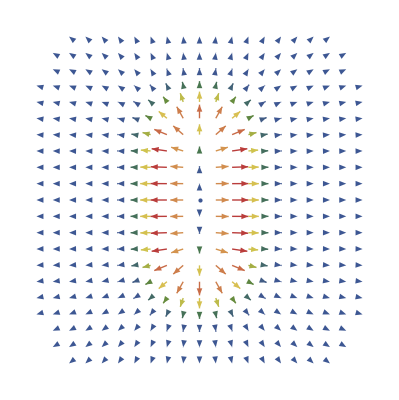

```mathematica
VectorFieldPlot[flux/.τ->.08,{ξ,-3,3},{η,-3,3},PlotPoints-> 21,ColorFunction->ColorData["DarkRainbow"]]
```

An example of the vector field as a function of position at time = 0.2, but with more control over the appearance of the arrows.

```mathematica
Needs["VectorFieldPlots`"];
vplots = Table[VectorFieldPlot[flux/.τ->time,{ξ,-3,3},{η,-3,3},PlotPoints->21,PlotRange->{{-4,4},{-4,4}},Frame->True,MaxArrowLength->3,ScaleFactor-> None,ScaleFunction->(2#&),ColorFunction-> (Hue[0.25+0.75 #]&)],{time,.001,.2,.005}];
```

```mathematica
ListAnimate[vplots]
```

Interrupted

```mathematica
ListAnimate[Table[Show[cplots[[i]],vplots[[i]],PlotRange->3.5{{-1,1},{-1,1}}],{i,1,Length[cplots]}]]
```